```mathematica
M=Transpose[{{(1-fu)^2(1-fp^2),fu(1-fp)(1-fu),fu(1-fp)(1-fu),fp^2(1-fu)^2,fp*fu*(1-fu),fp*fu(1-fu),fu^2},{(1-fp^2)(1-fu)fd,(1-fp)(1-fu)(1-fd),fu*fd(1-fp),fd(1-fu)fp^2,(1-fu)(1-fd)fp,fu*fd*fp,fu(1-fd)},{(1-fp^2)(1-fu)fd,fu*fd(1-fp),(1-fp)(1-fu)(1-fd),fd(1-fu)fp^2,fu*fd*fp,(1-fu)(1-fd)fp,fu(1-fd)},{2fp(1-fp)(1-fu)^2fdep,fdep(1-fp)(1-fu)fu,fdep*fu*(1-fu)(1-fp),(1-fu)^2(2(1-fdep)fp(1-fp)+fp^2+(1-fp)^2),fu(1-fu)(fp+(1-fp)(1-fdep)),fu(1-fu)(fp+(1-fp)(1-fdep)),fu^2},{fdep*fd(1-fu)(2fp(1-fp)),fdep(1-fd)(1-fu)(1-fp),fdep*fu*fd(1-fp),fd(1-fu)(fp^2+(1-fp)^2+2(1-fdep)fp(1-fp)),(1-fu)(1-fd)(fp+(1-fp)(1-fdep)),fu*fd(fp+(1-fp)(1-fdep)),fu(1-fd)},{2fdep(1-fu)fd*fp(1-fp),fu*fd*fdep(1-fp),fdep*(1-fu)*(1-fd)(1-fp),fd(1-fu)(fp^2+(1-fp)^2+2(1-fdep)fp(1-fp)),fu*fd(fp+(1-fdep)(1-fp)),(1-fu)(1-fd)(fp+(1-fdep)(1-fp)),fu(1-fd)},{2fdep*fd^2*fp(1-fp),fdep*fd(1-fd)(1-fp),fdep*fd(1-fd)(1-fp),fd^2(fp^2+(1-fp)^2+2(1-fdep)fp(1-fp)),fd(1-fd)(fp+(1-fp)(1-fdep)),fd(1-fd)(fp+(1-fp)(1-fdep)),(1-fd)^2}}]; (* fu is the probability of activity transitioning from the down to up state, fd is the probability of transitioning from the up to down state, fp is the sparsity of the plateau signal, and fdep is the probability of stochastic depotentiation in the Fusi model *)
```

```mathematica
MatrixForm[M]
```

((1-fp^2) (1-fu)^2 | fd (1-fp^2) (1-fu) | fd (1-fp^2) (1-fu) | 2 fdep (1-fp) fp (1-fu)^2 | 2 fd fdep (1-fp) fp (1-fu) | 2 fd fdep (1-fp) fp (1-fu) | 2 fd^2 fdep (1-fp) fp
(1-fp) (1-fu) fu | (1-fd) (1-fp) (1-fu) | fd (1-fp) fu | fdep (1-fp) (1-fu) fu | (1-fd) fdep (1-fp) (1-fu) | fd fdep (1-fp) fu | (1-fd) fd fdep (1-fp)
(1-fp) (1-fu) fu | fd (1-fp) fu | (1-fd) (1-fp) (1-fu) | fdep (1-fp) (1-fu) fu | fd fdep (1-fp) fu | (1-fd) fdep (1-fp) (1-fu) | (1-fd) fd fdep (1-fp)
fp^2 (1-fu)^2 | fd fp^2 (1-fu) | fd fp^2 (1-fu) | ((1-fp)^2+2 (1-fdep) (1-fp) fp+fp^2) (1-fu)^2 | fd ((1-fp)^2+2 (1-fdep) (1-fp) fp+fp^2) (1-fu) | fd ((1-fp)^2+2 (1-fdep) (1-fp) fp+fp^2) (1-fu) | fd^2 ((1-fp)^2+2 (1-fdep) (1-fp) fp+fp^2)
fp (1-fu) fu | (1-fd) fp (1-fu) | fd fp fu | ((1-fdep) (1-fp)+fp) (1-fu) fu | (1-fd) ((1-fdep) (1-fp)+fp) (1-fu) | fd ((1-fdep) (1-fp)+fp) fu | (1-fd) fd ((1-fdep) (1-fp)+fp)
fp (1-fu) fu | fd fp fu | (1-fd) fp (1-fu) | ((1-fdep) (1-fp)+fp) (1-fu) fu | fd ((1-fdep) (1-fp)+fp) fu | (1-fd) ((1-fdep) (1-fp)+fp) (1-fu) | (1-fd) fd ((1-fdep) (1-fp)+fp)
fu^2 | (1-fd) fu | (1-fd) fu | fu^2 | (1-fd) fu | (1-fd) fu | (1-fd)^2)

```mathematica
Total[M] //Simplify
```

{1,1,1,1,1,1,1}

```mathematica
m=M/.fdep->(fp+fa-fp*fa) /. fu->(1-c)fa /. fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[m]
```

((1-(1-c) fa)^2 (1-fp^2) | (1-c) (1-fa) (1-(1-c) fa) (1-fp^2) | (1-c) (1-fa) (1-(1-c) fa) (1-fp^2) | 2 (1-(1-c) fa)^2 (1-fp) fp (fa+fp-fa fp) | 2 (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | 2 (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | 2 (1-c)^2 (1-fa)^2 (1-fp) fp (fa+fp-fa fp)
(1-c) fa (1-(1-c) fa) (1-fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) | (1-c)^2 (1-fa) fa (1-fp) | (1-c) fa (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) (fa+fp-fa fp)
(1-c) fa (1-(1-c) fa) (1-fp) | (1-c)^2 (1-fa) fa (1-fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) | (1-c) fa (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) (fa+fp-fa fp)
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 ((1-fp)^2+fp^2+2 (1-fp) fp (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) ((1-fp)^2+fp^2+2 (1-fp) fp (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) ((1-fp)^2+fp^2+2 (1-fp) fp (1-fa-fp+fa fp)) | (1-c)^2 (1-fa)^2 ((1-fp)^2+fp^2+2 (1-fp) fp (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-c) fa (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) fa (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) (fp+(1-fp) (1-fa-fp+fa fp))
(1-c)^2 fa^2 | (1-c) (1-(1-c) (1-fa)) fa | (1-c) (1-(1-c) (1-fa)) fa | (1-c)^2 fa^2 | (1-c) (1-(1-c) (1-fa)) fa | (1-c) (1-(1-c) (1-fa)) fa | (1-(1-c) (1-fa))^2)

```mathematica
evals=Eigenvalues[m];
(*evalsreduce=evals/. fdep->fa /. fu->fa/(1-fa)*fd /. fd->1-(1+0)fa /. fa->fp;
evalsreduce2=evals/.fdep->fa /. fu->fa/(1-fa)*fd /. fd->(1-c)(1-fa) /. fa->fp;*)
```

```mathematica
evals/.fp->0.01 /.fa->.02/.c->.2
```

{1,0.2,0.2,0.04,0.1921,0.186352,0.997433}

```mathematica
evals
```

{1,c,c,c^2,-c (-1+fa) (-1+fp)^2,1/2 (1+c-3 c fa+2 c^2 fa-3 fa^2+6 c fa^2-3 c^2 fa^2+2 fa^3-4 c fa^3+2 c^2 fa^3-2 c fp-6 fa fp+10 c fa fp-4 c^2 fa fp+12 fa^2 fp-20 c fa^2 fp+8 c^2 fa^2 fp-6 fa^3 fp+12 c fa^3 fp-6 c^2 fa^3 fp-3 fp^2+c fp^2+12 fa fp^2-11 c fa fp^2+2 c^2 fa fp^2-15 fa^2 fp^2+22 c fa^2 fp^2-7 c^2 fa^2 fp^2+6 fa^3 fp^2-12 c fa^3 fp^2+6 c^2 fa^3 fp^2+2 fp^3-6 fa fp^3+4 c fa fp^3+6 fa^2 fp^3-8 c fa^2 fp^3+2 c^2 fa^2 fp^3-2 fa^3 fp^3+4 c fa^3 fp^3-2 c^2 fa^3 fp^3-(-1+fp)^2 √(1-2 c+c^2+6 c fa-10 c^2 fa+4 c^3 fa-6 fa^2-6 c fa^2+31 c^2 fa^2-22 c^3 fa^2+4 c^4 fa^2+4 fa^3+18 c fa^3-60 c^2 fa^3+50 c^3 fa^3-12 c^4 fa^3+9 fa^4-48 c fa^4+86 c^2 fa^4-64 c^3 fa^4+17 c^4 fa^4-12 fa^5+48 c fa^5-72 c^2 fa^5+48 c^3 fa^5-12 c^4 fa^5+4 fa^6-16 c fa^6+24 c^2 fa^6-16 c^3 fa^6+4 c^4 fa^6+4 fp-4 c fp-12 fa fp+16 c fa fp+8 c fa^2 fp-24 c^2 fa^2 fp+12 c^3 fa^2 fp+40 fa^3 fp-112 c fa^3 fp+120 c^2 fa^3 fp-56 c^3 fa^3 fp+8 c^4 fa^3 fp-60 fa^4 fp+188 c fa^4 fp-216 c^2 fa^4 fp+108 c^3 fa^4 fp-20 c^4 fa^4 fp+36 fa^5 fp-128 c fa^5 fp+168 c^2 fa^5 fp-96 c^3 fa^5 fp+20 c^4 fa^5 fp-8 fa^6 fp+32 c fa^6 fp-48 c^2 fa^6 fp+32 c^3 fa^6 fp-8 c^4 fa^6 fp+4 fp^2-24 fa fp^2+16 c fa fp^2+60 fa^2 fp^2-80 c fa^2 fp^2+24 c^2 fa^2 fp^2-80 fa^3 fp^2+160 c fa^3 fp^2-96 c^2 fa^3 fp^2+16 c^3 fa^3 fp^2+60 fa^4 fp^2-160 c fa^4 fp^2+144 c^2 fa^4 fp^2-48 c^3 fa^4 fp^2+4 c^4 fa^4 fp^2-24 fa^5 fp^2+80 c fa^5 fp^2-96 c^2 fa^5 fp^2+48 c^3 fa^5 fp^2-8 c^4 fa^5 fp^2+4 fa^6 fp^2-16 c fa^6 fp^2+24 c^2 fa^6 fp^2-16 c^3 fa^6 fp^2+4 c^4 fa^6 fp^2)),1/2 (1+c-3 c fa+2 c^2 fa-3 fa^2+6 c fa^2-3 c^2 fa^2+2 fa^3-4 c fa^3+2 c^2 fa^3-2 c fp-6 fa fp+10 c fa fp-4 c^2 fa fp+12 fa^2 fp-20 c fa^2 fp+8 c^2 fa^2 fp-6 fa^3 fp+12 c fa^3 fp-6 c^2 fa^3 fp-3 fp^2+c fp^2+12 fa fp^2-11 c fa fp^2+2 c^2 fa fp^2-15 fa^2 fp^2+22 c fa^2 fp^2-7 c^2 fa^2 fp^2+6 fa^3 fp^2-12 c fa^3 fp^2+6 c^2 fa^3 fp^2+2 fp^3-6 fa fp^3+4 c fa fp^3+6 fa^2 fp^3-8 c fa^2 fp^3+2 c^2 fa^2 fp^3-2 fa^3 fp^3+4 c fa^3 fp^3-2 c^2 fa^3 fp^3+(-1+fp)^2 √(1-2 c+c^2+6 c fa-10 c^2 fa+4 c^3 fa-6 fa^2-6 c fa^2+31 c^2 fa^2-22 c^3 fa^2+4 c^4 fa^2+4 fa^3+18 c fa^3-60 c^2 fa^3+50 c^3 fa^3-12 c^4 fa^3+9 fa^4-48 c fa^4+86 c^2 fa^4-64 c^3 fa^4+17 c^4 fa^4-12 fa^5+48 c fa^5-72 c^2 fa^5+48 c^3 fa^5-12 c^4 fa^5+4 fa^6-16 c fa^6+24 c^2 fa^6-16 c^3 fa^6+4 c^4 fa^6+4 fp-4 c fp-12 fa fp+16 c fa fp+8 c fa^2 fp-24 c^2 fa^2 fp+12 c^3 fa^2 fp+40 fa^3 fp-112 c fa^3 fp+120 c^2 fa^3 fp-56 c^3 fa^3 fp+8 c^4 fa^3 fp-60 fa^4 fp+188 c fa^4 fp-216 c^2 fa^4 fp+108 c^3 fa^4 fp-20 c^4 fa^4 fp+36 fa^5 fp-128 c fa^5 fp+168 c^2 fa^5 fp-96 c^3 fa^5 fp+20 c^4 fa^5 fp-8 fa^6 fp+32 c fa^6 fp-48 c^2 fa^6 fp+32 c^3 fa^6 fp-8 c^4 fa^6 fp+4 fp^2-24 fa fp^2+16 c fa fp^2+60 fa^2 fp^2-80 c fa^2 fp^2+24 c^2 fa^2 fp^2-80 fa^3 fp^2+160 c fa^3 fp^2-96 c^2 fa^3 fp^2+16 c^3 fa^3 fp^2+60 fa^4 fp^2-160 c fa^4 fp^2+144 c^2 fa^4 fp^2-48 c^3 fa^4 fp^2+4 c^4 fa^4 fp^2-24 fa^5 fp^2+80 c fa^5 fp^2-96 c^2 fa^5 fp^2+48 c^3 fa^5 fp^2-8 c^4 fa^5 fp^2+4 fa^6 fp^2-16 c fa^6 fp^2+24 c^2 fa^6 fp^2-16 c^3 fa^6 fp^2+4 c^4 fa^6 fp^2))}

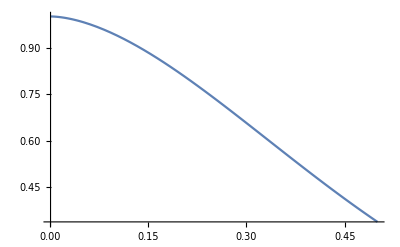

```mathematica
Plot[evals[[7]] /.fa->fp /.c->0.9,{fp,.001,.5}]
```

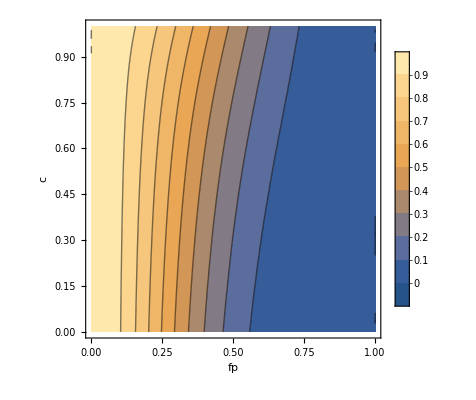

```mathematica
ContourPlot[evals[[7]]/.fa->fp ,{fp,0,1},{c,0,1},Axes->True,AxesLabel->{fp,c},PlotLegends->Automatic]
```

```mathematica
Series[evals[[7]]/.fa->fp,{fp,0,2}]
```

1/2 (1+√((-1+c)^2)+c)+1/2 (-5 c+2 c^2+(5 c-7 c^2+2 c^3)/(√((-1+c)^2))) fp+1/2 (-12+17 c-7 c^2-((-1+c) (-12-17 c+9 c^2))/(√((-1+c)^2))) fp^2+O[fp]^3

```mathematica
Refine[Series[evals[[7]]/.fa->fp,{fp,0,2}],c>0&&c<1] //Simplify
```

1+(-12+c^2) fp^2+O[fp]^3

```mathematica
λ2=evals[[7]];
mnum=m/. fp->.084 /.fa->.042 /.c->.8;
Eigenvalues[mnum]
```

{1.,0.965548,0.8,0.8,0.643053,0.64,0.637893}

```mathematica
evl=Eigenvectors[Transpose[mnum]];
evr=Eigenvectors[mnum];
evl1=Sqrt[7]*evl[[1]];
evl2=evl[[2]];
evr2=evr[[2]];
evr1=evr[[1]];
evr1=evr1/Total[evr1*evl1];
evr2=evr2/Total[evr2*evl2];
evr1 //Simplify
```

{0.625239,0.0245514,0.0245514,0.292525,0.0156846,0.0156846,0.001764}

```mathematica
w=(evr1[[4]]+evr1[[5]]+evr1[[6]]+evr1[[7]])/Total[evr1]
```

0.325659

```mathematica
Eigenvalues[m]
```

{1,c,c,c^2,-c (-1+fa) (-1+fp)^2,1/2 (1+c-3 c fa+2 c^2 fa-3 fa^2+6 c fa^2-3 c^2 fa^2+2 fa^3-4 c fa^3+2 c^2 fa^3-2 c fp-6 fa fp+10 c fa fp-4 c^2 fa fp+12 fa^2 fp-20 c fa^2 fp+8 c^2 fa^2 fp-6 fa^3 fp+12 c fa^3 fp-6 c^2 fa^3 fp-3 fp^2+c fp^2+12 fa fp^2-11 c fa fp^2+2 c^2 fa fp^2-15 fa^2 fp^2+22 c fa^2 fp^2-7 c^2 fa^2 fp^2+6 fa^3 fp^2-12 c fa^3 fp^2+6 c^2 fa^3 fp^2+2 fp^3-6 fa fp^3+4 c fa fp^3+6 fa^2 fp^3-8 c fa^2 fp^3+2 c^2 fa^2 fp^3-2 fa^3 fp^3+4 c fa^3 fp^3-2 c^2 fa^3 fp^3-(-1+fp)^2 √(1-2 c+c^2+6 c fa-10 c^2 fa+4 c^3 fa-6 fa^2-6 c fa^2+31 c^2 fa^2-22 c^3 fa^2+4 c^4 fa^2+4 fa^3+18 c fa^3-60 c^2 fa^3+50 c^3 fa^3-12 c^4 fa^3+9 fa^4-48 c fa^4+86 c^2 fa^4-64 c^3 fa^4+17 c^4 fa^4-12 fa^5+48 c fa^5-72 c^2 fa^5+48 c^3 fa^5-12 c^4 fa^5+4 fa^6-16 c fa^6+24 c^2 fa^6-16 c^3 fa^6+4 c^4 fa^6+4 fp-4 c fp-12 fa fp+16 c fa fp+8 c fa^2 fp-24 c^2 fa^2 fp+12 c^3 fa^2 fp+40 fa^3 fp-112 c fa^3 fp+120 c^2 fa^3 fp-56 c^3 fa^3 fp+8 c^4 fa^3 fp-60 fa^4 fp+188 c fa^4 fp-216 c^2 fa^4 fp+108 c^3 fa^4 fp-20 c^4 fa^4 fp+36 fa^5 fp-128 c fa^5 fp+168 c^2 fa^5 fp-96 c^3 fa^5 fp+20 c^4 fa^5 fp-8 fa^6 fp+32 c fa^6 fp-48 c^2 fa^6 fp+32 c^3 fa^6 fp-8 c^4 fa^6 fp+4 fp^2-24 fa fp^2+16 c fa fp^2+60 fa^2 fp^2-80 c fa^2 fp^2+24 c^2 fa^2 fp^2-80 fa^3 fp^2+160 c fa^3 fp^2-96 c^2 fa^3 fp^2+16 c^3 fa^3 fp^2+60 fa^4 fp^2-160 c fa^4 fp^2+144 c^2 fa^4 fp^2-48 c^3 fa^4 fp^2+4 c^4 fa^4 fp^2-24 fa^5 fp^2+80 c fa^5 fp^2-96 c^2 fa^5 fp^2+48 c^3 fa^5 fp^2-8 c^4 fa^5 fp^2+4 fa^6 fp^2-16 c fa^6 fp^2+24 c^2 fa^6 fp^2-16 c^3 fa^6 fp^2+4 c^4 fa^6 fp^2)),1/2 (1+c-3 c fa+2 c^2 fa-3 fa^2+6 c fa^2-3 c^2 fa^2+2 fa^3-4 c fa^3+2 c^2 fa^3-2 c fp-6 fa fp+10 c fa fp-4 c^2 fa fp+12 fa^2 fp-20 c fa^2 fp+8 c^2 fa^2 fp-6 fa^3 fp+12 c fa^3 fp-6 c^2 fa^3 fp-3 fp^2+c fp^2+12 fa fp^2-11 c fa fp^2+2 c^2 fa fp^2-15 fa^2 fp^2+22 c fa^2 fp^2-7 c^2 fa^2 fp^2+6 fa^3 fp^2-12 c fa^3 fp^2+6 c^2 fa^3 fp^2+2 fp^3-6 fa fp^3+4 c fa fp^3+6 fa^2 fp^3-8 c fa^2 fp^3+2 c^2 fa^2 fp^3-2 fa^3 fp^3+4 c fa^3 fp^3-2 c^2 fa^3 fp^3+(-1+fp)^2 √(1-2 c+c^2+6 c fa-10 c^2 fa+4 c^3 fa-6 fa^2-6 c fa^2+31 c^2 fa^2-22 c^3 fa^2+4 c^4 fa^2+4 fa^3+18 c fa^3-60 c^2 fa^3+50 c^3 fa^3-12 c^4 fa^3+9 fa^4-48 c fa^4+86 c^2 fa^4-64 c^3 fa^4+17 c^4 fa^4-12 fa^5+48 c fa^5-72 c^2 fa^5+48 c^3 fa^5-12 c^4 fa^5+4 fa^6-16 c fa^6+24 c^2 fa^6-16 c^3 fa^6+4 c^4 fa^6+4 fp-4 c fp-12 fa fp+16 c fa fp+8 c fa^2 fp-24 c^2 fa^2 fp+12 c^3 fa^2 fp+40 fa^3 fp-112 c fa^3 fp+120 c^2 fa^3 fp-56 c^3 fa^3 fp+8 c^4 fa^3 fp-60 fa^4 fp+188 c fa^4 fp-216 c^2 fa^4 fp+108 c^3 fa^4 fp-20 c^4 fa^4 fp+36 fa^5 fp-128 c fa^5 fp+168 c^2 fa^5 fp-96 c^3 fa^5 fp+20 c^4 fa^5 fp-8 fa^6 fp+32 c fa^6 fp-48 c^2 fa^6 fp+32 c^3 fa^6 fp-8 c^4 fa^6 fp+4 fp^2-24 fa fp^2+16 c fa fp^2+60 fa^2 fp^2-80 c fa^2 fp^2+24 c^2 fa^2 fp^2-80 fa^3 fp^2+160 c fa^3 fp^2-96 c^2 fa^3 fp^2+16 c^3 fa^3 fp^2+60 fa^4 fp^2-160 c fa^4 fp^2+144 c^2 fa^4 fp^2-48 c^3 fa^4 fp^2+4 c^4 fa^4 fp^2-24 fa^5 fp^2+80 c fa^5 fp^2-96 c^2 fa^5 fp^2+48 c^3 fa^5 fp^2-8 c^4 fa^5 fp^2+4 fa^6 fp^2-16 c fa^6 fp^2+24 c^2 fa^6 fp^2-16 c^3 fa^6 fp^2+4 c^4 fa^6 fp^2))}

```mathematica
(* symmetry matrix (exchange indices/swap pre and post) 1 (2 3) 4 (5 6) 7 *)
(*             1 0 0 0 0 0 0
             0 0 1 0 0 0 0
             0 1 0 0 0 0 0
    s=       0 0 0 1 0 0 0
             0 0 0 0 0 1 0
             0 0 0 0 1 0 0
             0 0 0 0 0 0 1  *)

s={{1,0,0,0,0,0,0},{0,0,1,0,0,0,0},{0,1,0,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,0,1,0},{0,0,0,0,1,0,0},{0,0,0,0,0,0,1}};
```

```mathematica
MatrixForm[s.m.s - m]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ppreb=Transpose[{{fp(1-fp)(1-fu)^2,0,fu(1-fu)(1-fp),fp^2(1-fu)^2,fp*fu(1-fu),fp*fu(1-fu),fu^2},{(1-fu)fd*fp(1-fp),0,fu*fd(1-fp),fd(1-fu)fp^2,(1-fu)(1-fd)fp,fu*fd*fp,fu(1-fd)},{fd(1-fu)fp(1-fp),0,(1-fu)(1-fd)(1-fp),fp^2*fd*(1-fu),fu*fd*fp,(1-fu)(1-fd)fp,fu(1-fd)},{fdep(1-fu)^2fp(1-fp),0,fdep*fu(1-fp)(1-fu),(1-fu)^2*fp(fp+(1-fdep)(1-fp)),fu*fp(1-fu),fu(1-fu)(fp+(1-fdep)(1-fp)),fu^2},{fdep*fd(1-fu)fp(1-fp),0,fdep*fu*fd(1-fp),fd(1-fu)fp(fp+(1-fp)(1-fdep)),fp(1-fu)(1-fd),fu*fd(fp+(1-fp)(1-fdep)),fu(1-fd)},{fdep*fd(1-fu)fp(1-fp),0,fdep(1-fu)(1-fd)(1-fp),fd(1-fu)fp(fp+(1-fp)(1-fdep)),fp*fu*fd,(1-fu)(1-fd)(fp+(1-fp)(1-fdep)),fu(1-fd)},{fdep*fd^2fp(1-fp),0,fdep*fd(1-fd)(1-fp),fd^2fp(fp+(1-fdep)(1-fp)),fp*fd(1-fd),fd(1-fd)(fp+(1-fp)(1-fdep)),(1-fd)^2}}]/.fdep->fa+fp-fa*fp/. fu->(1-c)fa /.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[ppreb]
```

((1-(1-c) fa)^2 (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa)^2 (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa)^2 (1-fp) fp (fa+fp-fa fp)
0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa (1-(1-c) fa) (1-fp) | (1-c)^2 (1-fa) fa (1-fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) | (1-c) fa (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) (fa+fp-fa fp)
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-c) fa (1-(1-c) fa) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-c) (1-(1-c) (1-fa)) (1-fa) fp
(1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) fa (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) (fp+(1-fp) (1-fa-fp+fa fp))
(1-c)^2 fa^2 | (1-c) (1-(1-c) (1-fa)) fa | (1-c) (1-(1-c) (1-fa)) fa | (1-c)^2 fa^2 | (1-c) (1-(1-c) (1-fa)) fa | (1-c) (1-(1-c) (1-fa)) fa | (1-(1-c) (1-fa))^2)

```mathematica
pprep=Transpose[{{fp(1-fp)(1-fu)^2,0,fu(1-fu)fp(1-fp),fp^2(1-fu)^2,fp*fu(1-fu),fp^2*fu(1-fu),fp*fu^2},{fp(1-fp)fd(1-fu),0,fu*fd*fp(1-fp),fp^2*fd(1-fu),fp(1-fu)(1-fd),fp^2*fu*fd,fp*fu(1-fd)},{fp(1-fp)fd(1-fu),0,fp(1-fp)(1-fu)(1-fd),fp^2*fd(1-fu),fp*fu*fd,fp^2(1-fu)(1-fd),fp*fu(1-fd)},{fdep*fp(1-fp)(1-fu)^2,0,fdep*fp*fu(1-fu)(1-fp),fp(1-fu)^2(fp+(1-fdep)(1-fp)),fp*fu(1-fu),fp*fu(1-fu)(fp+(1-fdep)(1-fp)),fp*fu^2},{fdep*fp(1-fp)fd(1-fu),0,fdep*fp(1-fp)*fu*fd,fp*fd(1-fu)(fp+(1-fdep)(1-fp)),fp(1-fd)(1-fu),fp*fu*fd(fp+(1-fp)(1-fdep)),fp*fu(1-fd)},{fdep*fd(1-fu)*fp(1-fp),0,fdep*fp(1-fd)(1-fu)(1-fp),fp*fd(1-fu)(fp+(1-fdep)(1-fp)),fp*fu*fd,fp(1-fu)(1-fd)(fp+(1-fp)(1-fdep)),fp*fu(1-fd)},{fdep*fd^2*fp(1-fp),0,fdep*fp(1-fp)*fd*(1-fd),fp*fd^2(fp+(1-fdep)(1-fp)),fp*fd(1-fd),fp*fd(1-fd)(fp+(1-fdep)(1-fp)),fp(1-fd)^2}}]/.fdep->fa+fp-fa*fp/. fu->(1-c)fa /.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[s.pprep.s]
```

((1-(1-c) fa)^2 (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa)^2 (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa)^2 (1-fp) fp (fa+fp-fa fp)
(1-c) fa (1-(1-c) fa) (1-fp) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp | (1-c)^2 (1-fa) fa (1-fp) fp | (1-c) fa (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) fp (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) fp (fa+fp-fa fp)
0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp^2 | (1-(1-c) (1-fa)) (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa) fa fp^2 | (1-c) fa (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) (1-(1-c) (1-fa)) (1-fa) fp
(1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-(1-c) (1-fa))^2 fp)

```mathematica
ppostp=s.pprep.s;
```

```mathematica
psimbp=Transpose[{{0,0,0,fp^2(1-fu)^2,fp^2*fu(1-fu),fp*fu(1-fu),fp*fu^2},{0,0,0,fp^2*fd(1-fu),fp^2(1-fu)(1-fd),fp*fu*fd,fp*fu(1-fd)},{0,0,0,fp^2fd(1-fu),fp^2fu*fd,fp(1-fd)(1-fu),fp*fu(1-fd)},{0,0,0,fp^2(1-fu)^2,fp^2*fu(1-fu),fp*fu(1-fu),fp*fu^2},{0,0,0,fp^2*fd(1-fu),fp^2(1-fu)(1-fd),fp*fu*fd,fp*fu(1-fd)},{0,0,0,fp^2*fd(1-fu),fp^2*fu*fd,fp(1-fd)(1-fu),fp*fu(1-fd)},{0,0,0,fp^2*fd^2,fp^2*fd(1-fd),fp(1-fd)fd,fp(1-fd)^2}}]/.fdep->fa+fp-fa*fp/. fu->(1-c)fa /.fd->(1-c)(1-fa);
```

```mathematica
MatrixForm[psimbp]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa)^2 fp^2
(1-c) fa (1-(1-c) fa) fp^2 | (1-(1-c) (1-fa)) (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa) fa fp^2 | (1-c) fa (1-(1-c) fa) fp^2 | (1-(1-c) (1-fa)) (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa) fa fp^2 | (1-c) (1-(1-c) (1-fa)) (1-fa) fp^2
(1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) (1-(1-c) (1-fa)) (1-fa) fp
(1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-(1-c) (1-fa))^2 fp)

```mathematica
mnumc0=m/.fp->.084/.c->0/.fa->.042  ;
ppostpnumc0=ppostp /.fp->.084/.c->0/.fa->.042 ;
pprebnumc0=ppreb  /.fp->.084/.c->0/.fa->.042 ;
evc0=Eigenvectors[mnumc0];
evr1numc0=evc0[[1]]/Total[evc0[[1]]] ;
psimbpnumc0=psimbp/.fp->.084/.c->0/.fa->.042 ;
mtnumc0=Table[Which[t==0,IdentityMatrix[7],t≠0,MatrixPower[mnumc0,t]],{t,0,150}];
```

```mathematica
compbpnumc0=Indexed[mtnumc0,tpost+1].ppostpnumc0.Indexed[mtnumc0,tpre-tpost ].pprebnumc0.evr1numc0;
```

```mathematica
copmbpnumc0=Indexed[mtnumc0,tpre+1].pprebnumc0.Indexed[mtnumc0,tpost-tpre].ppostpnumc0.evr1numc0;
```

```mathematica
cosbpnumc0=Indexed[mtnumc0,tpost+1].psimbpnumc0.evr1numc0;
```

```mathematica
xdnumbc0[t1_,t2_]=Which[t1==t2,cosbpnumc0/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2 ,t1<t2,copmbpnumc0/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2,t1>t2,(compbpnumc0/(.084(.084+.042-.084*.042))) /.tpre->t1/.tpost->t2];
```

```mathematica
pwbpc0=Table[1-(xdnumbc0[t1,t2])[[1]]-(xdnumbc0[t1,t2])[[2]]-(xdnumbc0[t1,t2])[[3]],{t1,0,100},{t2,0,100}];
```

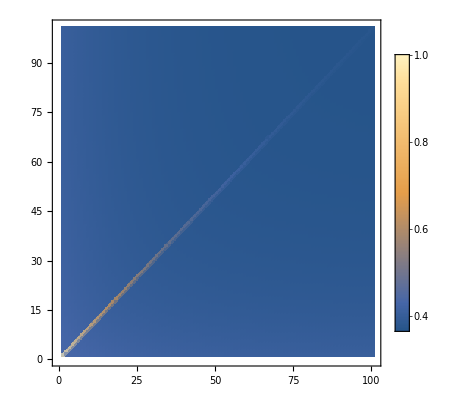

```mathematica
ListDensityPlot[pwbpc0,PlotLegends->Automatic,PlotRange->{0,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["pwdtb_fusitcorr_fp084_fa042_c0.csv",pwbpc0];
```

```mathematica
mnumc8=m/.fp->.084/.c->0.8/.fa->.042  ;
ppostpnumc8=ppostp /.fp->.084/.c->0.8/.fa->.042 ;
pprebnumc8=ppreb  /.fp->.084/.c->0.8/.fa->.042 ;
evc8=Eigenvectors[mnumc8];
evr1numc8=evc8[[1]]/Total[evc8[[1]]] ;
psimbpnumc8=psimbp/.fp->.084/.c->0.8/.fa->.042 ;
mtnumc8=Table[Which[t==0,IdentityMatrix[7],t≠0,MatrixPower[mnumc8,t]],{t,0,150}];
```

```mathematica
compbpnumc8=Indexed[mtnumc8,tpost+1].ppostpnumc8.Indexed[mtnumc8,tpre-tpost ].pprebnumc8.evr1numc8;
```

```mathematica
copmbpnumc8=Indexed[mtnumc8,tpre+1].pprebnumc8.Indexed[mtnumc8,tpost-tpre].ppostpnumc8.evr1numc8;
cosbpnumc8=Indexed[mtnumc8,tpost+1].psimbpnumc8.evr1numc8;

xdnumbc8[t1_,t2_]=Which[t1==t2,cosbpnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2 ,t1<t2,copmbpnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2,t1>t2,(compbpnumc8/(.084(.084+.042-.084*.042))) /.tpre->t1/.tpost->t2];
```

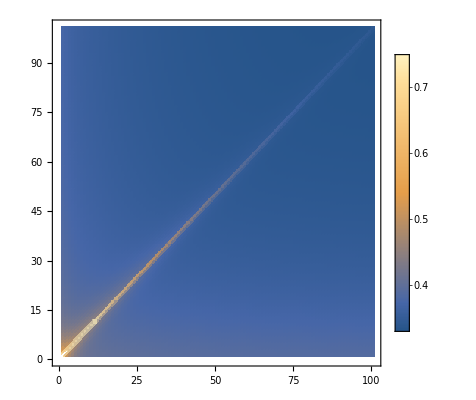

```mathematica
pwbpc8=Table[1-(xdnumbc8[t1,t2])[[1]]-(xdnumbc8[t1,t2])[[2]]-(xdnumbc8[t1,t2])[[3]],{t1,0,100},{t2,0,100}];
ListDensityPlot[pwbpc8,PlotLegends->Automatic,PlotRange->{0,.75}]
```

```mathematica
Export["pwdtb_fusitcorr_fp084_fa042_c8.csv",pwbpc8];
```

```mathematica
pprepnumc8=pprep  /.fp->.084/.c->0.8/.fa->.042 ;
psimppnumc8=fp*(m/.fp->1)/.fp->.084/.c->0.8/.fa->.042 ;
```

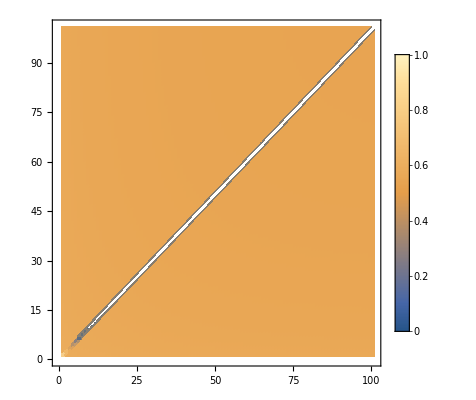

```mathematica
compppnumc8=Indexed[mtnumc8,tpost+1].ppostpnumc8.Indexed[mtnumc8,tpre-tpost ].pprepnumc8.evr1numc8;
copmppnumc8=Indexed[mtnumc8,tpre+1].pprepnumc8.Indexed[mtnumc8,tpost-tpre].ppostpnumc8.evr1numc8;
cosppnumc8=Indexed[mtnumc8,tpost+1].psimppnumc8.evr1numc8;
xdnumppc8[t1_,t2_]=Which[t1==t2,cosppnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2 ,t1<t2,copmppnumc8/(.084(.084+.042-.084*.042))/.tpre->t1 /.tpost->t2,t1>t2,(compppnumc8/(.084(.084+.042-.084*.042))) /.tpre->t1/.tpost->t2];
pwppc8=Table[1-(xdnumppc8[t1,t2])[[1]]-(xdnumppc8[t1,t2])[[2]]-(xdnumppc8[t1,t2])[[3]],{t1,0,100},{t2,0,100}];
ListDensityPlot[pwppc8,PlotLegends->Automatic,PlotRange->{0,1}]
Export["pwdtp_fusitcorr_fp084_fa042_c8.csv",pwppc8];
```

```mathematica
MatrixForm[pprep]
```

((1-(1-c) fa)^2 (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa)^2 (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa)^2 (1-fp) fp (fa+fp-fa fp)
0 | 0 | 0 | 0 | 0 | 0 | 0
(1-c) fa (1-(1-c) fa) (1-fp) fp | (1-c)^2 (1-fa) fa (1-fp) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp | (1-c) fa (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) fp (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) fp (fa+fp-fa fp)
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-c) fa (1-(1-c) fa) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-c) (1-(1-c) (1-fa)) (1-fa) fp
(1-c) fa (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa) fa fp^2 | (1-(1-c) (1-fa)) (1-(1-c) fa) fp^2 | (1-c) fa (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-(1-c) (1-fa))^2 fp)

```mathematica
MatrixForm[ppostp]
```

((1-(1-c) fa)^2 (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp | (1-(1-c) fa)^2 (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c) (1-fa) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa)^2 (1-fp) fp (fa+fp-fa fp)
(1-c) fa (1-(1-c) fa) (1-fp) fp | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp | (1-c)^2 (1-fa) fa (1-fp) fp | (1-c) fa (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-(1-c) (1-fa)) (1-(1-c) fa) (1-fp) fp (fa+fp-fa fp) | (1-c)^2 (1-fa) fa (1-fp) fp (fa+fp-fa fp) | (1-c) (1-(1-c) (1-fa)) (1-fa) (1-fp) fp (fa+fp-fa fp)
0 | 0 | 0 | 0 | 0 | 0 | 0
(1-(1-c) fa)^2 fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-c) (1-fa) (1-(1-c) fa) fp^2 | (1-(1-c) fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-fa) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa)^2 fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp^2 | (1-(1-c) (1-fa)) (1-(1-c) fa) fp^2 | (1-c)^2 (1-fa) fa fp^2 | (1-c) fa (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-(1-c) (1-fa)) (1-(1-c) fa) fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c)^2 (1-fa) fa fp (fp+(1-fp) (1-fa-fp+fa fp)) | (1-c) (1-(1-c) (1-fa)) (1-fa) fp (fp+(1-fp) (1-fa-fp+fa fp))
(1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) fa (1-(1-c) fa) fp | (1-c)^2 (1-fa) fa fp | (1-(1-c) (1-fa)) (1-(1-c) fa) fp | (1-c) (1-(1-c) (1-fa)) (1-fa) fp
(1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c)^2 fa^2 fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-c) (1-(1-c) (1-fa)) fa fp | (1-(1-c) (1-fa))^2 fp)

```mathematica
fpnum=.0836;
fanum=.0836;
fusi23=Range[91];
fusi24=Range[91];
fusi23minusw=Range[91];
fusi24minusw=Range[91];
For[i=1,i<92,i++,
cnum=.01*(i-1);
mnumcx=m/.fp->fpnum/.c->cnum/.fa->fanum;
evalsnumcx=Eigenvalues[mnumcx];
evlnumcx=Eigenvectors[Transpose[mnumcx]];
evrnumcx=Eigenvectors[mnumcx];
evrnum1cx=evrnumcx[[1]]/Total[evrnumcx[[1]]];
ppostnumcx=ppostp /.fp->fpnum/.c->cnum/.fa->fanum ;
pprebnumcx=ppreb /.fp->fpnum/.c->cnum/.fa->fanum;
psimbnumcx=psimbp/.fp->fpnum/.c->cnum/.fa->fanum ;
mtnumcx=Table[Which[t==0,IdentityMatrix[7],t≠0,MatrixPower[mnumcx,t]],{t,0,150}];

copmbnumcx=Indexed[mtnumcx,tpre+1].pprebnumcx.Indexed[mtnumcx,tpost-tpre].ppostnumcx.evrnum1cx;
compbnumcx=Indexed[mtnumcx,tpost+1].ppostnumcx.Indexed[mtnumcx,tpre-tpost ].pprebnumcx.evrnum1cx;
cosbnumcx=Indexed[mtnumcx,tpost+1].psimbnumcx.evrnum1cx;
xdnumbcx[t1_,t2_]=Which[t1==t2,cosbnumcx/(fp(fp+fa-fp*fa))/.tpre->t1 /.tpost->t2 /. fp->fpnum /.fa-> fanum ,t1<t2,copmbnumcx/(fp(fp+fa-fp*fa))/.tpre->t1 /.tpost->t2/. fp->fpnum /.fa-> fanum ,t1>t2,(compbnumcx/(fp(fp+fa-fp*fa))) /.tpre->t1/.tpost->t2 /. fp->fpnum /.fa-> fanum ];
fusi23[[i]]=1-(xdnumbcx[2,3])[[1]]-(xdnumbcx[2,3])[[2]]-(xdnumbcx[2,3])[[3]];
fusi24[[i]]=1-(xdnumbcx[2,4])[[1]]-(xdnumbcx[2,4])[[2]]-(xdnumbcx[2,4])[[3]];
meanw=1-evrnum1cx[[1]]-evrnum1cx[[2]]-evrnum1cx[[3]];
fusi23minusw[[i]]=fusi23[[i]]-meanw;
fusi24minusw[[i]]=fusi24[[i]]-meanw;
];
```

```mathematica
Export["fusi23_fp0836_fa0836.csv",fusi23];
Export["fusi24_fp0836_fa0836.csv",fusi24];
Export["fusi23minusw_fp0836_fa0836.csv",fusi23minusw];
Export["fusi24minusw_fp0836_fa0836.csv",fusi24minusw];
```